```mathematica
(* http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 *)

year = 2016;
(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[h_?NumericQ,a_?NumericQ,d_]:= ( (* params: hour of day*100, solar panel angle in degrees, date, returns misalignment with the sun in radians *)

(**** sunPos = SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[d,{h/100}]];*)
sunPos = sunPositions[[h]];

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = 0 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)

directPower[h_?NumericQ,a_?NumericQ,d_]  := ( (* param: hour of day*100, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[h,a,d]; (* solar zenith (misalignment) in radians *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

dayAngle := Function[ (* params: day of month, month, returns optimal angle for this day *)

date = DateObject[{year,#2,#1}];

position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,date];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,date];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[date,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,10}
];
(* Times 100 so the sum starts closer to the real sunUpHour, and not floors it to an integer when calculating the sum. Otherwise weird jumps in graphs appear when the sunUpHour jumps one hour *)

(* Find for which angle of the solar panels this value is maximal,starting at 50 *)

a/. FindMaximum[
Sum[directPower[h,a,date],{h,1,Length[sunPositions],10}]
,{a,50,0,90}, AccuracyGoal->5][[2]]
]

monthAngle := Function [ (* params: month, returns optimal angle for a specific month by taking the average  *)
(* Count how many days are in this month *)
days = With[{first=DateObject[{year,#1,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]] ;
Sum[dayAngle[x,#1],{x,1,days}]/days
]


(******************************** END OF FUNCTIONS  ********************************)
(*angle[1575,0,DateObject[{2016,12,20}]]*180/Pi*)
(*DiscretePlot3D[angle[h,x,DateObject[{2016,12,20}]]*180/Pi,{h,500,2300,10},{x,0,90,10},ImageSize -> Large, AxesLabel -> {"Hour of day", "Panel angle"}]*)
(*angle[1400,40,DateObject[{2016,7,18}]]*180/Pi
directPower[1400,30,DateObject[{2016,7,18}]]*)
(*directPower[1500,0,DateObject[{2016,7,18}]]
directPower[1500,10,DateObject[{2016,7,18}]]
 DiscretePlot[directPower[x,0,DateObject[{2016,7,18}]],{x,500,2300,10},ImageSize -> Large] 
 DiscretePlot[directPower[x,10,DateObject[{2016,7,18}]],{x,500,2300,10},ImageSize -> Large] 
 sumOverDay[0,DateObject[{2016,7,18}]] 
 sumOverDay[10,DateObject[{2016,7,18}]] *)

(* DiscretePlot[sumOverDay[a,DateObject[{2016,7,18}]],{a,0,90,10}] *)
(* NMinimize[{directPower[1400,x,DateObject[{2016,7,18}]],0≤ x ≤ 90},x] *)
(*DiscretePlot3D[directPower[h,a,DateObject[{2016,7,18}]],{h,500,2300,50},{a,0,90,5}]

FindMaximum[directPower[1400,x,DateObject[{2016,7,18}]],{x,0,0,90}, AccuracyGoal->5] //Timing
directPower[1400,50,DateObject[{2016,7,18}]]*)
(* DiscretePlot[sumOverDay[x,DateObject[{2016,7,18}]],{x,0,90,10}] *)

(*NMaximize[{sumOverDay[x,DateObject[{2016,7,18}]],0≤ x ≤ 90},x] //Timing*) (* took 60 secs, .02 for FindMaximum *)
(*FindMaximum[sumOverDay[x,DateObject[{2016,7,18}]],{x,50,0,90}, AccuracyGoal->5]
sumOverDay[0,DateObject[{2016,7,18}]]*)

dayAngle[18,9] //Timing (* takes 30 secs, because SunPosition takes 0.015 *)

(*DiscretePlot[dayAngle[15,x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "optimal angle at 15th"}] //Timing*)

(***** END OF DEBUG ******)

(* Graph for a day *)
(* date = DateObject[{2016,7,18}];
 AbsoluteTiming[DiscretePlot[sumOverDay[x,date],{x,0,90,10},ImageSize->Large,AxesLabel -> {"Solar panel angle", "Total of sun power, W/m^2"}] ] *)

(* Graph for a month *)
 (* month = 9;
days = With[{first=DateObject[{year,month,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
AbsoluteTiming[DiscretePlot[dayAngle[a,month],{a,1,days},ImageSize->Large,AxesLabel -> {"Day", "Optimal angle"}]] *)

(* Graph for this year *)
(* AbsoluteTiming[DiscretePlot[monthAngle[x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}] ] *)
```

{5.79688,48.4258}

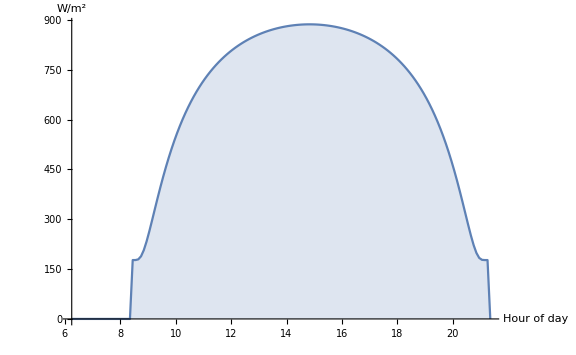
```mathematica
8/6,30 panel angle-Graphics-
```

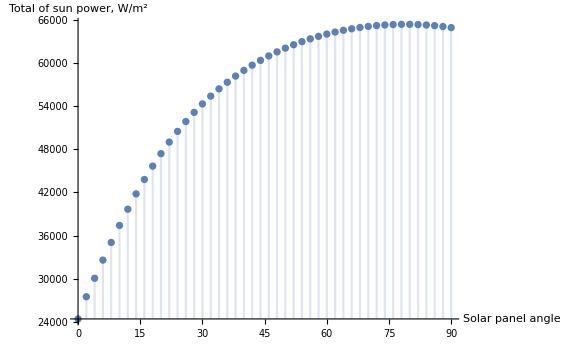
```mathematica
december first:-Graphics-
```

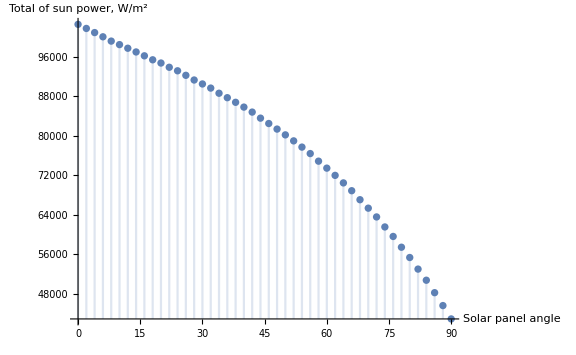
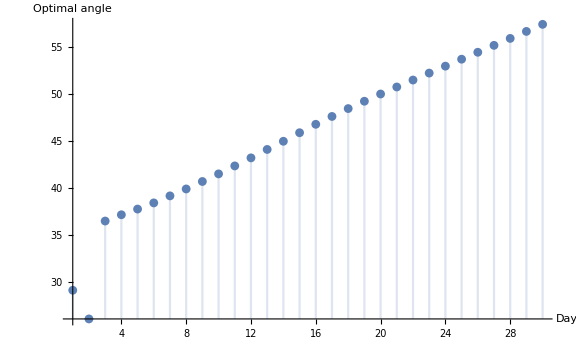
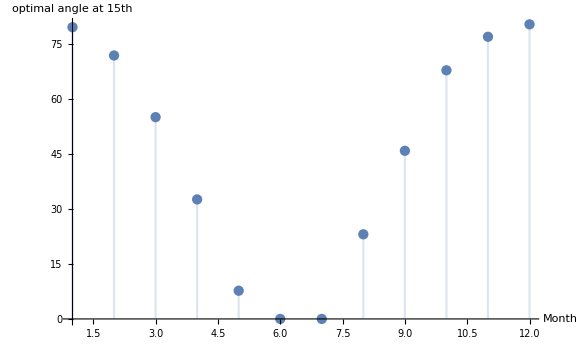
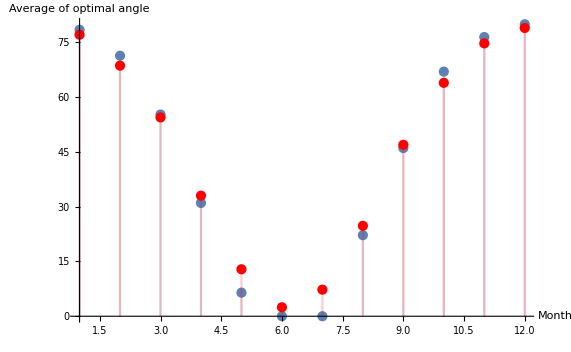
```mathematica
20/6 -Graphics-
september: -Graphics-
Every 15th day of the month: -Graphics-
18/7-Graphics3D-
20/6-Graphics3D-
20/12 -Graphics3D-
comparison with old 1-Cos[i] (red) -Graphics-
```